```mathematica
(*1. Force directory and import your row string data*)SetDirectory[NotebookDirectory[]];
rawData=Import["numerical_solution_final.txt","Table"];

If[rawData===$Failed,Print["Error: Data file not found!"],cleanData=Rest[rawData];
(*2. Select rows matching t=0.5 precisely (with a small numerical tolerance)*)tPlane05=Select[cleanData,Abs[#[[3]]-0.5]<0.001&];
(*3. Structure into spatial matrix coordinates {x,y,u}*)plotData05=Table[{row[[1]],row[[2]],row[[4]]},{row,tPlane05}];
(*4. Render 3D Spatial Plane Graph*)surfacePlot=ListPlot3D[plotData05,PlotStyle->Directive[Specularity[White,20]],ColorFunction->"Rainbow",Mesh->None,AxesLabel->{Style["x",Bold,FontSize->16],Style["t",Bold,FontSize->16],Style["u(x,y,t)",Bold,FontSize->16]},ImageSize->Medium];
Print[surfacePlot];]
```

-Graphics3D-

```mathematica
If[rawData=!=$Failed,(*Function to grab space data at any user-defined time target*)getTimeSnapshot[targetT_]:=Module[{filtered,structured},filtered=Select[cleanData,Abs[#[[3]]-targetT]<0.001&];
structured=Table[{row[[1]],row[[2]],row[[4]]},{row,filtered}];
ListPlot3D[structured,ColorFunction->"TemperatureMap",PlotRange->{0,1.1},Mesh->None,AxesLabel->{"x","y","u"},PlotLabel->Row[{"Time t = ",targetT}],ImageSize->Medium]];
(*Generate frames at start,quarter-cycle,and half-cycle*)frame1=getTimeSnapshot[0.0];
frame2=getTimeSnapshot[0.25];
frame3=getTimeSnapshot[0.5];
(*Combine them neatly row-by-row*)Print[GraphicsGrid[{{frame1,frame2,frame3}},ImageSize->950]];]
```

-Graphics-

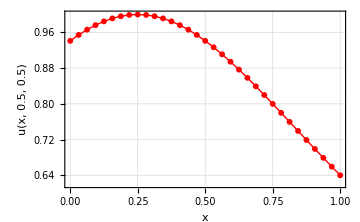

```mathematica
SetDirectory[NotebookDirectory[]];

rawData=Import["numerical_solution_final.txt","Table"];



If[rawData===$Failed,Print["Error loading data file!"],cleanData=Rest[rawData];
(*Filter rows where y is approx 0.5 AND t is approx 0.5*)sliceData=Select[cleanData,(Abs[#[[2]]-0.5]<0.03&&Abs[#[[3]]-0.5]<0.03)&];
(*Sort coordinates by x value to ensure a clean sequential line plot*)sortedSlice=SortBy[Table[{row[[1]],row[[4]]},{row,sliceData}],First];
(*Generate 2D Profile Curve Plot*)plot2DProfile=ListLinePlot[sortedSlice,PlotStyle->{Thick,Red},PlotMarkers->{Automatic,6},GridLines->Automatic,Frame->True,FrameLabel->{"x",Style["u(x, 0.5, 0.5)"],Bold,FontSize->16},ImageSize->Medium];
Print[plot2DProfile];]
```

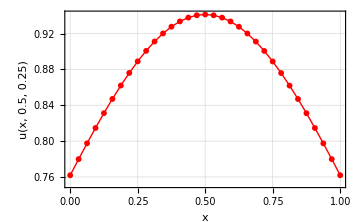

```mathematica
SetDirectory[NotebookDirectory[]];
rawData=Import["numerical_solution_final.txt","Table"];

If[rawData===$Failed,Print["Error loading data file!"],cleanData=Rest[rawData];
(*Filter rows where y is approx 0.5 AND t is approx 0.25*)sliceData=Select[cleanData,(Abs[#[[2]]-0.5]<0.03&&Abs[#[[3]]-0.25]<0.03)&];
(*Sort coordinates by x value to ensure a clean sequential line plot*)sortedSlice=SortBy[Table[{row[[1]],row[[4]]},{row,sliceData}],First];
(*Generate 2D Profile Curve Plot*)plot2DProfile=ListLinePlot[sortedSlice,PlotStyle->{Thick,Red},PlotMarkers->{Automatic,6},GridLines->Automatic,Frame->True,FrameLabel->{"x",Style["u(x, 0.5, 0.25)",Bold,FontSize->16]},ImageSize->Medium];
Print[plot2DProfile];]
```

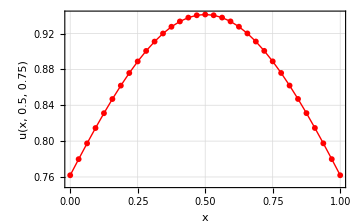

```mathematica
SetDirectory[NotebookDirectory[]];
rawData=Import["numerical_solution_final.txt","Table"];

If[rawData===$Failed,Print["Error loading data file!"],cleanData=Rest[rawData];
(*Filter rows where y is approx 0.5 AND t is approx 0.75*)sliceData=Select[cleanData,(Abs[#[[2]]-0.5]<0.03&&Abs[#[[3]]-0.75]<0.03)&];
(*Sort coordinates by x value to ensure a clean sequential line plot*)sortedSlice=SortBy[Table[{row[[1]],row[[4]]},{row,sliceData}],First];
(*Generate 2D Profile Curve Plot*)plot2DProfile=ListLinePlot[sortedSlice,PlotStyle->{Thick,Red},PlotMarkers->{Automatic,6},GridLines->Automatic,Frame->True,FrameLabel->{"x",Style["u(x, 0.5, 0.75)",Bold,FontSize->16]},ImageSize->Medium];
Print[plot2DProfile];]
```

```mathematica
SetDirectory[NotebookDirectory[]];
rawData=Import["numerical_solution_final.txt","Table"];

If[rawData===$Failed,Print["Error loading data file!"],cleanData=Rest[rawData];
(*Filter rows where y is approx 0.5 AND t is approx 0.5*)sliceData=Select[cleanData,(Abs[#[[2]]-0.5]<0.03&&Abs[#[[3]]-0.5]<0.03)&];
(*Sort coordinates by x value to ensure a clean sequential line plot*)sortedSlice=SortBy[Table[{row[[1]],row[[4]]},{row,sliceData}],First];
(*Generate 2D Profile Curve Plot*)plot2DProfile=ListLinePlot[sortedSlice,PlotStyle->{Thick,Red},PlotMarkers->{Automatic,6},GridLines->Automatic,Frame->True,FrameLabel->{"x",Style["u(x, 0.5, 0.5)"],Bold, FontSize->16},ImageSize->Medium];
Print[plot2DProfile];]
```

-Graphics-

LineLegend::optx: Unknown option LegendBackground→color in ….

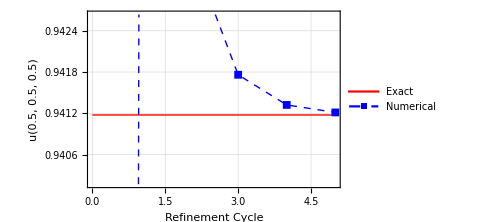

```mathematica
cycles=Table[i,{i,0,5}];



(*Replace these lists with the exact numbers printed in your final loop table*)

exactValsCenter={0.941176,0.941176,0.941176,0.941176,0.941176,0.941176};

numValsCenter={0.656814,0.955246,0.943625,0.941760,0.941322,0.941213};



plotCenter=ListLinePlot[{Thread[{cycles,exactValsCenter}],Thread[{cycles,numValsCenter}]},PlotStyle->{{Red,Thick},{Blue,Thick,Dashed}},PlotMarkers->{None,{Automatic,8}},(*Moves the legend inside using coordinates {x,y} from 0 to 1*)PlotLegends->Placed[LineLegend[{"Exact","Numerical"},LegendBackground->White,LegendBorder->Black,PlotRange->{{0,5},{0.1,1}},LabelStyle->{FontFamily->"Arial",11}],{0.82,0.82} (*Adjusted position:top-right corner inside*)],GridLines->Automatic,Frame->True,FrameLabel->{"Refinement Cycle","u(0.5, 0.5, 0.5)"},ImageSize->Medium]
```

LineLegend::optx: Unknown option LegendBackground→color in ….

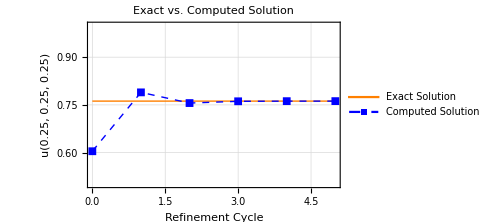

```mathematica
cycles=Table[i,{i,0,5}];

(*Exact and numerical data arrays*)
exactValsCenter={0.761905,0.761905,0.761905,0.761905,0.761905,0.761905};
numValsCenter={0.604269,0.789380,0.755749,0.761324,0.761761,0.761870};

plotCenter=ListLinePlot[{Thread[{cycles,exactValsCenter}],Thread[{cycles,numValsCenter}]},PlotStyle->{{Orange,Thick},{Blue,Thick,Dashed}},PlotMarkers->{None,{Automatic,8}},(*Option B:Clear boundaries that isolate the asymptotic convergence window*)PlotRange->{{0,5},{0.5,1}},PlotLegends->Placed[LineLegend[{"Exact Solution","Computed Solution"},LegendBackground->White,LegendBorder->Black,LabelStyle->{FontFamily->"Arial",11}],{0.72,0.82}],GridLines->Automatic,Frame->True,PlotLabel->Style["Exact vs. Computed Solution",Bold,14],FrameLabel->{"Refinement Cycle","u(0.25, 0.25, 0.25)"},ImageSize->Medium]
```

LineLegend::optx: Unknown option LegendBackground→color in ….

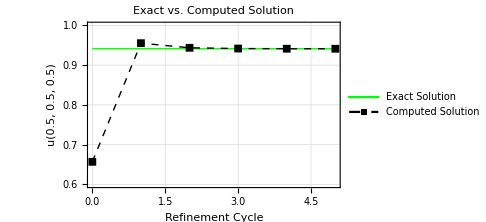

```mathematica
cycles=Table[i,{i,0,5}];

(*Exact and numerical data arrays*)
exactValsCenter={0.941176,0.941176,0.941176,0.941176,0.941176,0.941176};
numValsCenter={0.656814,0.955246,0.943625,0.941760,0.941322,0.941213};

plotCenter=ListLinePlot[{Thread[{cycles,exactValsCenter}],Thread[{cycles,numValsCenter}]},PlotStyle->{{Green,Thick},{Black,Thick,Dashed}},PlotMarkers->{None,{Automatic,8}},(*Option B:Clear boundaries that isolate the asymptotic convergence window*)PlotRange->{{0,5},{0.6,1}},PlotLegends->Placed[LineLegend[{"Exact Solution","Computed Solution"},LegendBackground->White,LegendBorder->Black,LabelStyle->{FontFamily->"Arial",11}],{0.72,0.52}],GridLines->Automatic,Frame->True,PlotLabel->Style["Exact vs. Computed Solution",Bold,14],FrameLabel->{"Refinement Cycle","u(0.5, 0.5, 0.5)"},ImageSize->Medium]
```

LineLegend::optx: Unknown option LegendBackground→color in ….

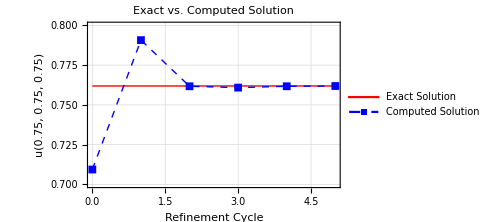

```mathematica
cycles=Table[i,{i,0,5}];

(*Exact and numerical data arrays*)
exactValsCenter={0.761905,0.761905,0.761905,0.761905,0.761905,0.761905};
numValsCenter={0.709360,.790733,0.761708,0.760870,0.761709,0.761862};

plotCenter=ListLinePlot[{Thread[{cycles,exactValsCenter}],Thread[{cycles,numValsCenter}]},PlotStyle->{{Red,Thick},{Blue,Thick,Dashed}},PlotMarkers->{None,{Automatic,8}},(*Option B:Clear boundaries that isolate the asymptotic convergence window*)PlotRange->{{0,5},{0.7,0.8}},PlotLegends->Placed[LineLegend[{"Exact Solution","Computed Solution"},LegendBackground->White,LegendBorder->Black,LabelStyle->{FontFamily->"Arial",11}],{0.72,0.82}],GridLines->Automatic,Frame->True,PlotLabel->Style["Exact vs. Computed Solution",Bold,14],FrameLabel->{"Refinement Cycle","u(0.75, 0.75, 0.75)"},ImageSize->Medium]
```

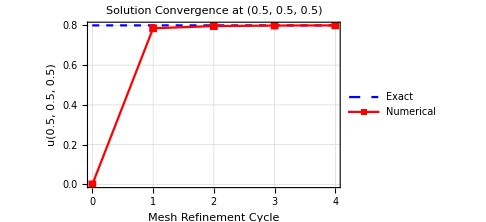

```mathematica
cycles=Table[i,{i,0,4}];

(*Replace these lists with the exact numbers printed in your final loop table*)
exactValsCenter={0.800000,0.800000,0.800000,0.800000,0.800000};
numValsCenter={0.000000,0.785420,0.796350,0.799140,0.799938};

plotCenter=ListLinePlot[{Thread[{cycles,exactValsCenter}],Thread[{cycles,numValsCenter}]},PlotStyle->{{Blue,Thick,Dashed},{Red,Thick}},PlotMarkers->{None,{Automatic,8}},PlotLegends->LineLegend[{"Exact","Numerical"}],GridLines->Automatic,Frame->True,FrameLabel->{"Mesh Refinement Cycle","u(0.5, 0.5, 0.5)"},PlotLabel->Style["Solution Convergence at (0.5, 0.5, 0.5)",Bold,13],ImageSize->Medium]
```

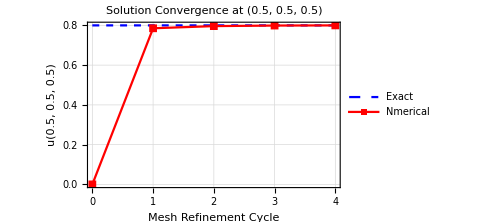

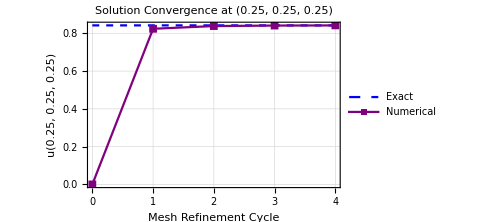

```mathematica
cycles=Table[i,{i,0,4}];

exactValsLower={0.842105,0.842105,0.842105,0.842105,0.842105};
numValsLower={0.000000,0.824100,0.838500,0.841200,0.841932};

plotLower=ListLinePlot[{Thread[{cycles,exactValsLower}],Thread[{cycles,numValsLower}]},PlotStyle->{{Blue,Thick,Dashed},{Purple,Thick}},PlotMarkers->{None,{Automatic,8}},PlotLegends->LineLegend[{"Exact","Numerical"}],GridLines->Automatic,Frame->True,FrameLabel->{"Mesh Refinement Cycle","u(0.25, 0.25, 0.25)"},PlotLabel->Style["Solution Convergence at (0.25, 0.25, 0.25)",Bold,13],ImageSize->Medium]
```

LineLegend::optx: Unknown option LegendBackground→color in ….

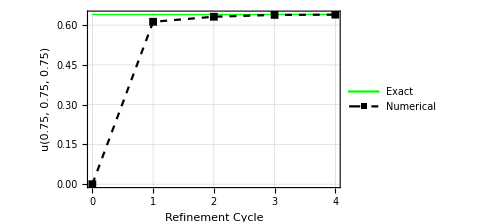

```mathematica
cycles=Table[i,{i,0,4}];

exactValsUpper={0.640000,0.640000,0.640000,0.640000,0.640000};
numValsUpper={0.000000,0.612500,0.631500,0.638400,0.639395};

plotUpper=ListLinePlot[{Thread[{cycles,exactValsUpper}],Thread[{cycles,numValsUpper}]},PlotStyle->{{Green,Thick,Thick},{Darker[Black],Dashed}},PlotMarkers->{None,{Automatic,8}},(*Places the boxed legend inside the graph layout*)PlotLegends->Placed[LineLegend[{"Exact","Numerical"},LegendBackground->White,LegendBorder->Black,LabelStyle->{FontFamily->"Arial",11}],{0.82,0.82} (*Coordinates inside the frame mapping to the top-right*)],GridLines->Automatic,Frame->True,FrameLabel->{"Refinement Cycle","u(0.75, 0.75, 0.75)"},ImageSize->Medium]
```

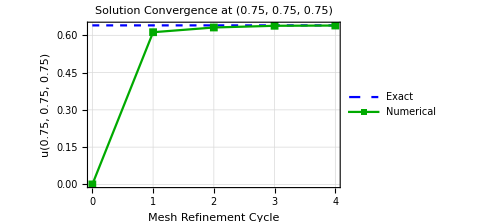

```mathematica
cycles=Table[i,{i,0,4}];

exactValsUpper={0.640000,0.640000,0.640000,0.640000,0.640000};
numValsUpper={0.000000,0.612500,0.631500,0.638400,0.639395};

plotUpper=ListLinePlot[{Thread[{cycles,exactValsUpper}],Thread[{cycles,numValsUpper}]},PlotStyle->{{Blue,Thick,Dashed},{Darker[Green],Thick}},PlotMarkers->{None,{Automatic,8}},PlotLegends->LineLegend[{"Exact","Numerical"}],GridLines->Automatic,Frame->True,FrameLabel->{"Mesh Refinement Cycle","u(0.75, 0.75, 0.75)"},PlotLabel->Style["Solution Convergence at (0.75, 0.75, 0.75)",Bold,13],ImageSize->Medium]
```

Calculated Convergence Slope: -0.966865

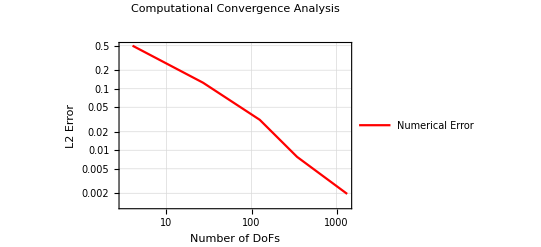

```mathematica
(*1. Define your refinement data from your C++ output*)(*Let's assume you have 5 cycles,so 5 data points*)refinements={0,1,2,3,4};
dofs={4,27,125,343,1331}; (*Replace with your actual DoF counts*)
errors={0.5,0.125,0.03125,0.0078125,0.001953}; (*Replace with your L2 errors*)

(*2. Prepare the data for Log-Log plot*)
logData=Transpose[{Log[dofs],Log[errors]}];

(*3. Calculate the slope using LinearModelFit*)
lm=LinearModelFit[logData,x,x];
slope=lm["BestFitParameters"][[2]];
Print["Calculated Convergence Slope: ",slope];

(*4. Plotting*)
convergencePlot=ListLogLogPlot[{Transpose[{dofs,errors}]},PlotStyle->{Red,Thick},Joined->True,Frame->True,FrameLabel->{"Number of DoFs","L2 Error"},PlotLabel->Style["Computational Convergence Analysis",Bold,14],GridLines->Automatic,PlotLegends->{"Numerical Error"},Epilog->{Blue,Dashed,Text[Style["Slope: "<>ToString[NumberForm[slope,{2,2}]],Blue,14],{10,0.05}]}];
Print[convergencePlot];
```

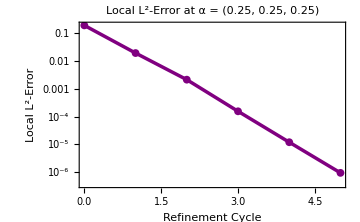

```mathematica
(*---Data Setup for Alpha---*)cyclesAlpha=Table[i,{i,0,5}];
errorsAlpha={1.9628 * 10^(-1),1.9683*10^(-2),2.1556*10^(-3),1.5562*10^(-4),1.1915*10^(-5),9.3315*10^(-7)};
errorDataAlpha=Thread[{cyclesAlpha,errorsAlpha}];

(*---Plot Generation---*)
plotAlpha=ListLogPlot[errorDataAlpha,Joined->True,PlotStyle->{Purple,AbsoluteThickness[2.5]},PlotMarkers->{Automatic,8},GridLines->Automatic,Frame->True,FrameLabel->{"Refinement Cycle","Local L^2-Error"},PlotRange->All,ImageSize->Medium,PlotLabel->Style["Local L^2-Error at α = (0.25, 0.25, 0.25)",Bold,13]]
```

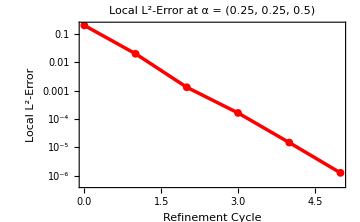

```mathematica
(*---Data Setup for Alpha---*)cyclesAlpha=Table[i,{i,0,5}];
errorsAlpha={1.9628 * 10^(-1),1.9683*10^(-2),1.3064*10^(-3),1.6343*10^(-4),1.4822*10^(-5),1.2739*10^(-6)};
errorDataAlpha=Thread[{cyclesAlpha,errorsAlpha}];

(*---Plot Generation---*)
plotAlpha=ListLogPlot[errorDataAlpha,Joined->True,PlotStyle->{Red,AbsoluteThickness[2.5]},PlotMarkers->{Automatic,8},GridLines->Automatic,Frame->True,FrameLabel->{"Refinement Cycle","Local L^2-Error"},PlotRange->All,ImageSize->Medium,PlotLabel->Style["Local L^2-Error at β = (0.5, 0.5, 0.5)",Bold,13]]
```

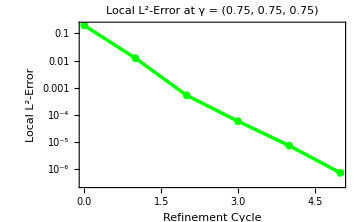

```mathematica
(*---Data Setup for Alpha---*)cyclesAlpha=Table[i,{i,0,5}];
errorsAlpha={1.9628 * 10^(-1),1.2143*10^(-2),5.2232*10^(-4),5.8305*10^(-5),7.3594*10^(-6),7.3085*10^(-7)};
errorDataAlpha=Thread[{cyclesAlpha,errorsAlpha}];

(*---Plot Generation---*)
plotAlpha=ListLogPlot[errorDataAlpha,Joined->True,PlotStyle->{Green,AbsoluteThickness[2.5]},PlotMarkers->{Automatic,8},GridLines->Automatic,Frame->True,FrameLabel->{"Refinement Cycle","Local L^2-Error"},PlotRange->All,ImageSize->Medium,PlotLabel->Style["Local L^2-Error at γ = (0.75, 0.75, 0.75)",Bold,13]]
```